```mathematica
SOI=Import["/users/pp/Desktop/soi.txt", "table"];
TSID=Import["/users/pp/Desktop/tsi.txt", "table"];
QBO=Import["/users/pp/Desktop/qbo20.txt", "table"];
QBO70=Import["/users/pp/Desktop/qbo.txt", "table"];
CW=Import["/users/pp/Desktop/cw.txt", "table"];
CW1=Import["/users/pp/Desktop/cw1_1930.txt", "table"];
CW0=Import["/users/pp/Desktop/cw1.txt", "table"];
NINO34=Import["/users/pp/Desktop/nino34ke.txt", "table"];
tahiti=Import["/users/pp/Desktop/tahiti.txt", "table"];
darwin=Import["/users/pp/Desktop/darwin0.txt", "table"];
```

```mathematica
(* ################################### SIMPLIFIED VERY GOOD ##################################### *)
WinLowFilter = 212;    WinHiFilter = 9;
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter] - 1*MeanFilter[darwin[[All,2]],WinLowFilter]) - (1*MeanFilter[tahiti[[All,2]],WinHiFilter] - 1*MeanFilter[tahiti[[All,2]],WinLowFilter]); 
STRT=24; STRTY=1880+STRT/12; SEP=0.0; LNGTH=1603; ENDY=1880+LNGTH/12; (* 1603 STRT=590;   STRTY=1880+STRT/12; SEP=0.0; LNGTH=1190; ENDY=1880+LNGTH/12; *)
SOIT = Table[{1880+i/12, -0.034*R[[i]]+SEP},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
```

80.0069

{0.,-44.1774}

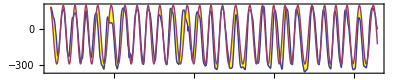

```mathematica
qbo[x_] :=  Cos[2.6956*(x+0.24*Sin[0.523*x+2.82]-0.07*Sin[0.12*x+0.2])+1.44] ; 
QBOM = Table[{1953.0+x, -240*qbo[73.0+x]-50},{x,1/12,61.25+1/12, 1/12}];  Q = MeanFilter[QBO[[All,2]],3];
QBOT = Table[{QBOM[[i,1]], Q[[i]]},{i,1,12*61.25+1, 1}];        
100*Correlation[QBOT,QBOM][[2,2]]
Variance[QBOT]-Variance[QBOM]
ListLinePlot[{QBOT, QBOM}, AspectRatio->0.2, Filling->{1->{{2},Yellow}}, Frame->True, Axes->False, PlotLegends->{"QBO", "Model"}]
```

80.1

{0.,-32.8793}

2.33056

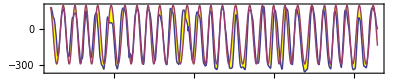

```mathematica
QB=2.696; qbo[x_] :=  Cos[QB*(x+0.24*Sin[0.523*x+2.82]-0.07*Sin[0.12*x+0.2])+1.44] ; 
QBOM = Table[{1953.0+x, -240*qbo[73.0+x]-50},{x,1/12,61.25+1/12, 1/12}];  Q = MeanFilter[QBO[[All,2]],3];
QBOT = Table[{QBOM[[i,1]], Q[[i]]},{i,1,12*61.25+1, 1}];        
100*Correlation[QBOT,QBOM][[2,2]]
Variance[QBOT]-Variance[QBOM]
2*Pi/QB
ListLinePlot[{QBOT, QBOM}, AspectRatio->0.2, Filling->{1->{{2},Yellow}}, Frame->True, Axes->False, PlotLegends->{"QBO", "Model"}]
```

70.2574

{1.85371×10^-8,13330.4}

6.47885

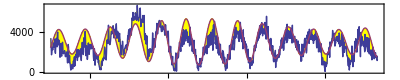

```mathematica
CW =0.9698; cw[x_] := Sin[CW*(x+2.)+ 0.119*Sin[0.36*(x+6.8)] +0.5] *(1+0.31*Sin[0.093*x-0.2]) ;  
CWM = Table[{1880+i, 1770*cw[i-1.3]+3000},{i,50,133+2/12, 1/12}];
100*Correlation[CW1,CWM][[2,2]]
Variance[CW1]-Variance[CWM]
2*Pi/CW
ListLinePlot[{CW1,CWM}, AspectRatio->0.2, Filling->{1->{{2},Yellow}}, Frame->True, Axes->False, PlotLegends->{"CW", "Model"}]
```

91.5396

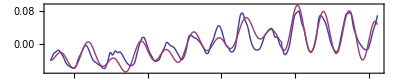

```mathematica
(* Number 1 *)
HALE:=0.5875; HALE2:=0.596;
tsi[x_] := +1.12*If[x<95.0,
                    0.8*(1.58*Cos[HALE*(x-0.029)] + 1.3*Cos[HALE/2*(x-6.7)]+0.22*Cos[HALE/3*(x+3.3)]),
                    1.0*(3.1*Cos[HALE2*(x-1.28)]+0.35*Cos[HALE/2*(x-3.92)]) ] +
                    2.4*Cos[2*Pi*x/153.0-1] ; 
TSDATA= 1*MeanFilter[TSID[[All,2]],0] - 0*MeanFilter[TSID[[All,2]],200]; 
TSIT = Table[{1880+i/12, 2.75*TSDATA[[i]]},{i,STRT,LNGTH,1}]; 
TSIM = Table[{1880.0+x, -0.015*(tsi[x+0.39])},{x,STRT/12,LNGTH/12, 1/12}];
100*Correlation[TSIT,TSIM][[2,2]]
ListLinePlot[{TSIT, TSIM}, AspectRatio->0.2, Frame->True, Axes->False, PlotLegends->{"TSI", "Model"}]
```

92.318

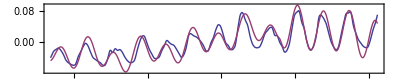

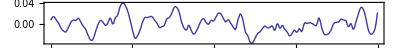

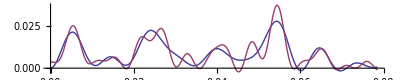

```mathematica
(* Number 2 *)
sigmoid[x_] := 1/(1+Exp[3.2*(x-94.1)]); 
HALE:=0.59; HALE2:=0.596;
tsi[x_] := +1.12*((sigmoid[x])*0.8*(2.2*Cos[HALE*(x-0.029)] + 1.3*Cos[HALE/2*(x-6.7)]+0.22*Cos[HALE/3*(x+3.3)]) +
                   (1-sigmoid[x])*1.0*(3.1*Cos[HALE2*(x-1.28)]+0.35*Cos[HALE/2*(x-3.92)])) +  
             2.4*Cos[2*Pi*x/153.0-1]; 
TSDATA= 1*MeanFilter[TSID[[All,2]],0] - 0*MeanFilter[TSID[[All,2]],200]; 
TSIT = Table[{1880+i/12, 2.75*TSDATA[[i]]},{i,STRT,LNGTH,1}]; 
TSIM = Table[{1880.0+x, -0.015*(tsi[x+0.39])},{x,STRT/12,LNGTH/12, 1/12}];
100*Correlation[TSIT,TSIM][[2,2]]
ListLinePlot[{TSIT, TSIM}, AspectRatio->0.2, Frame->True, Axes->False, PlotLegends->{"TSI", "Model"}] 
SDIF = TSIT[[All,2]]-TSIM[[All,2]];  
ListLinePlot[SDIF, Frame->True, Axes->True, PlotLegends->{"SOI-Model"}, AspectRatio->0.1] 
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,800,1200,400}],{ω,0,π/40},PlotRange->All,AspectRatio->0.2]
```

96.4614   31.3405

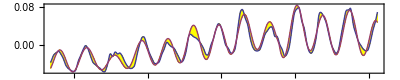

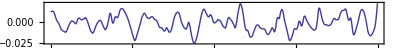

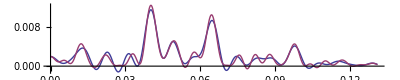

```mathematica
(* Number 3 *)
sigmoid[x_] := 1/(1+Exp[6*(x-94.0)]); 
HALE:=0.59; HALE2:=0.596;
tsi[x_] := +1.12*((sigmoid[x])*0.62*(2.7*Cos[HALE*(x-0.11)] + 0.7*Cos[HALE/2*(x-5.7)]+0.18*Cos[HALE/3*(x+3.8)]) +
                   (1-sigmoid[x])*0.99*(3.12*Cos[HALE2*(x-1.29)]+0.55*Cos[HALE/2*(x-7.0)])) +  
             2.42*Cos[2*Pi*x/153.1-1.0] +0.62*Cos[2*Pi*x/9.57+1.5] + 0.55*Cos[2*Pi*x/105.0+0.4] + 0*0.39*Cos[2*Pi*x/12.9+2.5]; 
TSDATA= 1*MeanFilter[TSID[[All,2]],0] - 0*MeanFilter[TSID[[All,2]],200]; 
TSIT = Table[{1880+i/12, 2.75*TSDATA[[i]]},{i,STRT,LNGTH,1}]; 
TSIM = Table[{1880.0+x, -0.015*(tsi[x+0.39])},{x,STRT/12,LNGTH/12, 1/12}];
OldCC = NewCC; NewCC = 100*Correlation[TSIT,TSIM][[2,2]]; Print[NewCC, "   ", NewCC-OldCC];
ListLinePlot[{TSIT, TSIM}, AspectRatio->0.2, Filling->{1->{{2},Yellow}}, Frame->True, Axes->False, PlotLegends->{"TSI", "Model"}] 
SDIF = TSIT[[All,2]]-TSIM[[All,2]];  
ListLinePlot[SDIF, Frame->True, Axes->True, PlotLegends->{"SOI-Model"}, AspectRatio->0.1] 
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,800,1200,400}],{ω,0,π/24},PlotRange->All,AspectRatio->0.2]
```

{char t,4.24094,-0.00141505, Years from,1880.5,to,2013.58,CC,56.6104,51.1616,-5.44879}

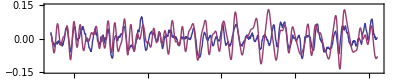

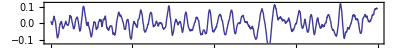

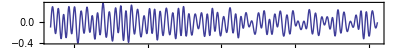

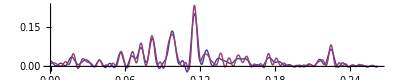

```mathematica
(* ################################### SIMPLIFIED VERY GOOD ##################################### *)
WinLowFilter = 220;    WinHiFilter = 8;
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter] - 1*MeanFilter[darwin[[All,2]],WinLowFilter]) - (1*MeanFilter[tahiti[[All,2]],WinHiFilter] - 1*MeanFilter[tahiti[[All,2]],WinLowFilter]); 
STRT=6; STRTY=1880+STRT/12; SEP=0.0; LNGTH=1603; ENDY=1880+LNGTH/12; (* 1603 STRT=590;   STRTY=1880+STRT/12; SEP=0.0; LNGTH=1190; ENDY=1880+LNGTH/12; *)
SOIT = Table[{1880+i/12, -0.034*R[[i]]+SEP},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 2.195;  dilate[x_] := -0*(0.185*Sin[0.07*x+0.9]+0.13*Cos[2*Pi*x+1.5]);  ClSh := 1002.32; (* + 0*0.008*DiracDelta[x-50.0] 1.98 *)
RHS[x_] := 0*(-0.2*Cos[4*Pi*x*1-0.009] - 0.2*Cos[2*Pi*x*1.0188-0.1]) + 
          2.8*(0.078*qbo[x+0.7]*(0.99+0.12*tsi[x-0.8])-
          0.026*cw[x+0.05]-0.000*tsi[x+4.1]-0.0055 -0.000002*x );
NDSolve[{y''[x]+(CF+0.35*tsi[x-0.8]-0.18*cw[x+0.6])*y[x] == RHS[x],  y'[52.0]==-0.01, y[52.0]==+0.03}, y, {x, 0, 260}];   
SOIM = Table[{1880.0+x, -0*0.03*Cos[2*Pi/4.5*x+1.0]+First[-0.5*y[x+dilate[x]+0.39] /. %]},{x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-0.15,0.15+SEP},Frame->True,Axes->False,  PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
SDIF = SOIT[[All,2]]-SOIM[[All,2]];  
ListLinePlot[SDIF, PlotRange->{-0.12,0.12}, Frame->True, Axes->True, PlotLegends->{"SOI-Model"}, AspectRatio->0.1] 
RHSD = Table[{1880+i/12, RHS[i/12]},{i,STRT,LNGTH,1}];
ListLinePlot[{RHSD}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"RHS"}]
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,800,1200,400}],{ω,0,π/12},PlotRange->All,AspectRatio->0.2]
```

{char t,4.22844,-0.0000186068, Years from,1880.5,to,2013.58,CC,26.7091,61.7584,35.0493}

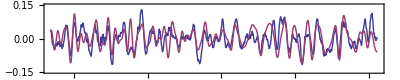

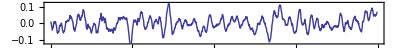

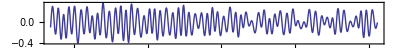

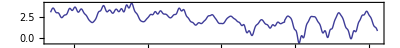

```mathematica
(* NUMBER 1 *)
(* ################################### SIMPLIFIED VERY GOOD ##################################### *)
WinLowFilter = 210;    WinHiFilter = 8;
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter] - 1*MeanFilter[darwin[[All,2]],WinLowFilter]) - (1*MeanFilter[tahiti[[All,2]],WinHiFilter] - 1*MeanFilter[tahiti[[All,2]],WinLowFilter]); 
STRT=6; STRTY=1880+STRT/12; SEP=0.0; LNGTH=1603; ENDY=1880+LNGTH/12; (* 1603 STRT=590;   STRTY=1880+STRT/12; SEP=0.0; LNGTH=1190; ENDY=1880+LNGTH/12; *)
SOIT = Table[{1880+i/12, -0.045*R[[i]]+SEP},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 2.208;  dilate[x_] := -(0.16*Sin[0.074*x+0.7]-0.0*Cos[2*Pi*x+1.5]); (* + 0*0.008*DiracDelta[x-50.0] 1.98 *)
Hill[x_] := CF+0.353*tsi[x-0.77]*(1+0.19*qbo[x+0.5])-0.2*cw[x+0.72];
RHS[x_] := 0*0.9*(-0.2*Cos[4*Pi*x*1-0.3] - 0.14*Cos[2*Pi*x-0.3]) + 2.7*(0.077*qbo[x+0.7]*(1+0.13*tsi[x-1.1])-
          0.025*cw[x+0.04]-0.0013*tsi[x+4.2]-0.005 +0.00000*x );
NDSolve[{y''[x]+Hill[x]*y[x] == RHS[x],  y'[52.0]==-0.023, y[52.0]==+0.016}, y, {x, 0, 260}];   
SOIM = Table[{1880.0+x, -0.034*Cos[2*Pi/4.518*x+1.6]+0.007*qbo[x+0.03]+ First[-0.49*y[1.0006*x+dilate[x]+0.41] /. %]},{x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-0.15,0.15+SEP},Frame->True,Axes->False,  PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
SDIF = SOIT[[All,2]]-SOIM[[All,2]];  
ListLinePlot[SDIF, PlotRange->{-0.12,0.12}, Frame->True, Axes->True, PlotLegends->{"SOI-Model"}, AspectRatio->0.1] 
RHSD = Table[{1880+i/12, RHS[i/12]},{i,STRT,LNGTH,1}];
ListLinePlot[{RHSD}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"RHS"}]
HillD = Table[{1880+i/12, Hill[i/12]},{i,STRT,LNGTH,1}];
ListLinePlot[{HillD}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"Hill"}]
(* Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,800,1200,400}],{ω,0,π/12},PlotRange->All,AspectRatio->0.2]  *)
```

{char t,4.51106,-0.0000207042, Years from,1880.5,to,2013.58,CC,37.9264,37.9264,0.}

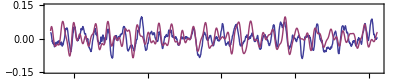

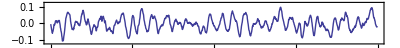

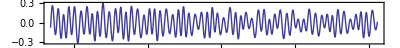

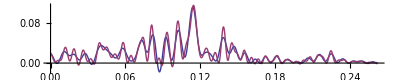

```mathematica
(* ################################### SIMPLIFIED VERY GOOD ##################################### *)
WinLowFilter = 220;    WinHiFilter = 8;
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter] - 1*MeanFilter[darwin[[All,2]],WinLowFilter]) - (1*MeanFilter[tahiti[[All,2]],WinHiFilter] - 1*MeanFilter[tahiti[[All,2]],WinLowFilter]); 
STRT=6; STRTY=1880+STRT/12; SEP=0.0; LNGTH=1603; ENDY=1880+LNGTH/12; (* 1603 STRT=590;   STRTY=1880+STRT/12; SEP=0.0; LNGTH=1190; ENDY=1880+LNGTH/12; *)
SOIT = Table[{1880+i/12, -0.034*R[[i]]+SEP},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 1.94;  dilate[x_] := -0*(0.185*Sin[0.07*x+0.9]+0.13*Cos[2*Pi*x+1.5]);  ClSh := 1002.32; (* + 0*0.008*DiracDelta[x-50.0] 1.98 *)
RHS[x_] := 0*(-0.2*Cos[4*Pi*x*1-0.009] - 0.2*Cos[2*Pi*x*1.0188-0.1]) + 
          2.0*(0.089*qbo[x+0.72]*(0.99+0.1*tsi[x-0.8])-
          0.026*cw[x+0.05]-0.000*tsi[x+4.1]-0.0055 -0.000002*x );
NDSolve[{y''[x]+(CF+0.05*tsi[x+0.2]-0.12*cw[x+0.6])*y[x] == RHS[x],  y'[52.0]==-0.01, y[52.0]==+0.03}, y, {x, 0, 260}];   
SOIM = Table[{1880.0+x, -0*0.03*Cos[2*Pi/4.5*x+1.0]+First[-0.5*y[x+dilate[x]+0.5] /. %]},{x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-0.15,0.15+SEP},Frame->True,Axes->False,  PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
SDIF = SOIT[[All,2]]-SOIM[[All,2]];  
ListLinePlot[SDIF, PlotRange->{-0.12,0.12}, Frame->True, Axes->True, PlotLegends->{"SOI-Model"}, AspectRatio->0.1] 
RHSD = Table[{1880+i/12, RHS[i/12]},{i,STRT,LNGTH,1}];
ListLinePlot[{RHSD}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"RHS"}]
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,800,1200,400}],{ω,0,π/12},PlotRange->All,AspectRatio->0.2]
```

{char t,4.23324,0.0000281368, Years from,1880.5,to,2013.58,CC,64.0166,64.0677,0.0511049}

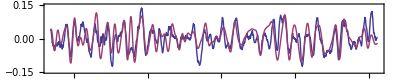

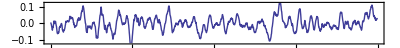

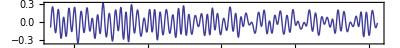

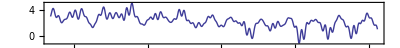

```mathematica
(* NUMBER 2  *)
(* ################################### SIMPLIFIED VERY GOOD ##################################### *)
WinLowFilter = 214;    WinHiFilter = 8;
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter] - 1*MeanFilter[darwin[[All,2]],WinLowFilter]) - (1*MeanFilter[tahiti[[All,2]],WinHiFilter] - 1*MeanFilter[tahiti[[All,2]],WinLowFilter]); 
STRT=6; STRTY=1880+STRT/12; SEP=0.0; LNGTH=1603; ENDY=1880+LNGTH/12; (* 1603 STRT=590;   STRTY=1880+STRT/12; SEP=0.0; LNGTH=1190; ENDY=1880+LNGTH/12; *)
SOIT = Table[{1880+i/12, -0.048*R[[i]]+SEP},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 2.203;  dilate[x_] := -(0.09*Sin[0.074*x+0.7]-0.0*Cos[2*Pi*x+1.5]); (* + 0*0.008*DiracDelta[x-50.0] 1.98 *)
Hill[x_] := CF+0.342*tsi[x-1.19]*(1+0.52*qbo[x+0.458])-0.38*cw[x+0.84];
RHS[x_] := -0*0.9*(-0.1*Cos[4*Pi*x+1.3] - 0.06*Cos[2*Pi*x-1.3]) + 2.75*(0.062*qbo[x+0.69]*(0.99+0.13*tsi[x-1.18])-
          0.026*cw[x+0.04]-0.0011*tsi[x+5.0]-0.0048 +0.00000*x );
NDSolve[{y''[x]+Hill[x]*y[x] == RHS[x-0.02],  y'[52.0]==-0.042, y[52.0]==+0.016}, y, {x, 0, 260}];   
SOIM = Table[{1880.0+x, -0.03*Cos[2*Pi/4.52*x+1.6]+0.0051*qbo[x+0.03]+ First[-0.52*y[1.0014*x+dilate[x]+0.38] /. %]},{x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-0.15,0.15+SEP},Frame->True,Axes->False,  PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
SDIF = SOIT[[All,2]]-SOIM[[All,2]];  
ListLinePlot[SDIF, PlotRange->{-0.12,0.12}, Frame->True, Axes->True, PlotLegends->{"SOI-Model"}, AspectRatio->0.1] 
RHSD = Table[{1880+i/12, RHS[i/12]},{i,STRT,LNGTH,1}];
ListLinePlot[{RHSD}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"RHS"}]
HillD = Table[{1880+i/12, Hill[i/12]},{i,STRT,LNGTH,1}];
ListLinePlot[{HillD}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"Hill"}]
(* Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,800,1200,400}],{ω,0,π/12},PlotRange->All,AspectRatio->0.2]  *)
```

{char t,4.23901,0.000945165, Years from,1880.17,to,2013.58,CC,65.3906,65.2623,-0.128313}

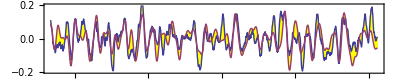

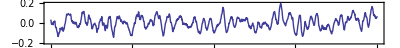

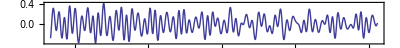

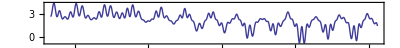

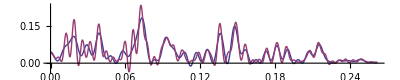

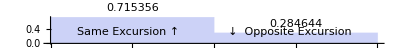

```mathematica
(* NUMBER 3  *)
(* ################################### SIMPLIFIED VERY GOOD ##################################### *)
WinLowFilter = 210;    WinHiFilter = 8;
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter] - 1*MeanFilter[darwin[[All,2]],WinLowFilter]) - (1*MeanFilter[tahiti[[All,2]],WinHiFilter] - 1*MeanFilter[tahiti[[All,2]],WinLowFilter]); 
STRT=2; STRTY=1880+STRT/12; SEP=0.0; LNGTH=1603; ENDY=1880+LNGTH/12; (* 1603 STRT=590;   STRTY=1880+STRT/12; SEP=0.0; LNGTH=1190; ENDY=1880+LNGTH/12; *)
SOIT = Table[{1880+i/12, -0.075*R[[i]]+SEP},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 2.197;  dilate[x_] := -(0.19*Sin[0.074*x-0.5]+0.0*Cos[2*Pi*x-0.2]); (* + 0*0.008*DiracDelta[x-50.0] 1.98 *)
OSC := 9.0786;     TR =52.01;
Hill[x_] := CF+0.359*tsi[x-1.53]*(1.03+0.62*qbo[x+0.43])-0*0.05*cw[x-2.2] ;
Osc[x_] := 0.042*(Cos[2*Pi/OSC*x+4.35]-Cos[4*Pi/OSC*x+2.14]) +0*0.03*Cos[2*Pi/7.3*x+0.5];
RHS[x_] :=+ 2.99*(0.061*qbo[x+0.72]*(1+0.16*tsi[x+0.64])- 0.032*cw[x+0.05]+0.0004*tsi[x+3.9]+0.0005 +0.000007*x-0*0.01*Osc[x-0.6] );  
NDSolve[{y''[x]+Hill[x]*y[x] == RHS[x-0.07],  y'[TR]==-0.01, y[TR]==+0.0052}, y, {x, 0, 260}];   
SOIM = Table[{1880.0+x, Osc[x]+ 0*0.01*tsi'[x-4.5]+First[-0.49*y[1.0008*x+dilate[x]+0.63] /. %]},{x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-0.2,0.2+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
SDIF = SOIT[[All,2]]-SOIM[[All,2]];  
ListLinePlot[SDIF, PlotRange->{-0.2,0.2}, Frame->True, Axes->True, PlotLegends->{"SOI-Model"}, AspectRatio->0.1] 
RHSD = Table[{1880+i/12, RHS[i/12]},{i,STRT,LNGTH,1}];
ListLinePlot[{RHSD}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"RHS"}]
HillD = Table[{1880+i/12, Hill[i/12]},{i,STRT,LNGTH,1}];
ListLinePlot[{HillD}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"Hill"}]
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,800,1200,400}],{ω,0,π/12},PlotRange->All,AspectRatio->0.2]
SBIN = Abs[Sign[SOIT[[All,2]]]- Sign[SOIM[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.05,  ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
```

{char t,4.23901,0.000118369, Years from,1880.17,to,2013.58,CC,73.8,72.8382,-0.96181}

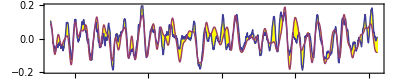

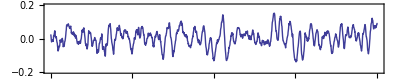

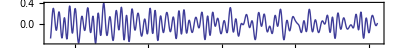

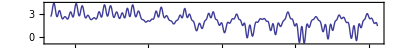

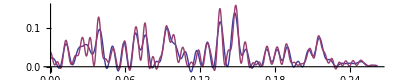

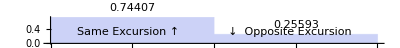

```mathematica
(* NUMBER 3  *)
(* ################################### SIMPLIFIED VERY GOOD ##################################### *)
WinLowFilter = 210;    WinHiFilter = 8;  (* 8 *)
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter]-1*MeanFilter[darwin[[All,2]],WinLowFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]-1*MeanFilter[tahiti[[All,2]],WinLowFilter]); 
STRT=2; STRTY=1880+STRT/12; SEP=0.0; LNGTH=1603; ENDY=1880+LNGTH/12; (* 1603 STRT=590;   STRTY=1880+STRT/12; SEP=0.0; LNGTH=1190; ENDY=1880+LNGTH/12; *)
SOIT = Table[{1880+i/12, -0.073*R[[i]]+SEP},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 2.197;  dilate[x_] := -(0.19*Sin[0.074*x-0.5]+0.0*Cos[2*Pi*x-0.2]);
OSC := 9.08;     TR=52.01;
Hill[x_] := CF+0.357*tsi[x-1.55]*(1.03+0.62*qbo[x+0.43])  ;
Osc[x_] := 0.039*(Cos[2*Pi/OSC*x+4.45]-Cos[4*Pi/OSC*x+2.18]) +0.033*Cos[2*Pi/7.3*x+0.47] - 0.026*Cos[2*Pi*x/27.3-0.6];
RHS[x_] :=+ 2.98*(0.06*qbo[x+0.71]*(0.98+0.16*tsi[x+0.62])-0.032*cw[x+0.04]+0.0006*tsi[x+3.9]+0.0008+0.000007*x );  
SOLN=NDSolve[{y''[x]+Hill[x]*y[x] == RHS[x-0.08],  y'[TR]==-0.01, y[TR]==+0.0052}, y, {x, 0, 260}];   
SOIM=Table[{1880.0+x, Osc[x]+0.009*tsi'[x-4.4]-0.009*qbo[x-0.6]+First[-0.49*y[1.0008*x+dilate[x]+0.63] /. SOLN]},{x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-0.2,0.2+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
SDIF = SOIT[[All,2]]-SOIM[[All,2]];  
ListLinePlot[SDIF, PlotRange->{-0.2,0.2}, Frame->True, Axes->True, PlotLegends->{"SOI-Model"}, AspectRatio->0.2] 
RHSD = Table[{1880+i/12, RHS[i/12]},{i,STRT,LNGTH,1}];
ListLinePlot[{RHSD}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"RHS"}]
HillD = Table[{1880+i/12, Hill[i/12]},{i,STRT,LNGTH,1}];
ListLinePlot[{HillD}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"Hill"}]
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,800,1200,400}],{ω,0,π/12},PlotRange->All,AspectRatio->0.2]
SBIN = Abs[Sign[SOIT[[All,2]]]- Sign[SOIM[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.05,  ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
```

```mathematica
0.009/0.073
```

0.123288

{char t,4.23901,-0.00176169, Years from,1880.17,to,2013.58,CC,60.012,73.9049,13.8929}

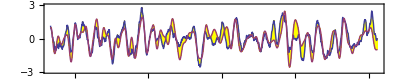

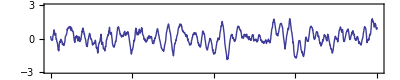

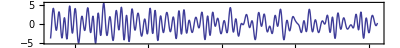

-Graphics-

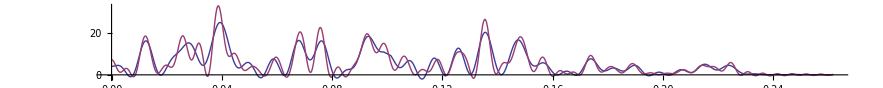

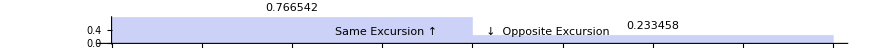

```mathematica
(* NUMBER 3  *)
(* ################################### From data ##################################### *)
WinLowFilter = 214;    WinHiFilter = 11;  (* 8 *)
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter]-1*MeanFilter[darwin[[All,2]],WinLowFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]-1*MeanFilter[tahiti[[All,2]],WinLowFilter]); 
STRT=2; STRTY=1880+STRT/12; SEP=0.0; LNGTH=1603; ENDY=1880+LNGTH/12; (* 1603 STRT=590;   STRTY=1880+STRT/12; SEP=0.0; LNGTH=1190; ENDY=1880+LNGTH/12; *)
SOIT = Table[{1880+i/12, -1.1*R[[i]]+SEP},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 2.197;  dilate[x_] := -(0.19*Sin[0.074*x-0.5]+0.0*Cos[2*Pi*x-0.2]);
OSC := 9.08;     TR=52.01;
Hill[x_] := CF+0.357*tsi[x-1.55]*(1.03+0.62*qbo[x+0.43])  ;
Osc[x_] := 0.534*(Cos[2*Pi/OSC*x+4.45]-Cos[4*Pi/OSC*x+2.18]) +0.438*Cos[2*Pi/7.3*x+0.47] - 0.356*Cos[2*Pi*x/27.3-0.6];
RHS[x_] :=+ 2.98*(0.8219*qbo[x+0.71]*(0.98+0.16*tsi[x+0.62])-0.438*cw[x+0.04]+0.0082*tsi[x+3.9]+0.011+0.0001*x -0*0.014*tsi'[x+5.6]-0*0.15*qbo'[x]);  
SOLN=NDSolve[{y''[x]+Hill[x]*y[x] == RHS[x-0.08],  y'[TR]==-0.02, y[TR]==+0.03}, y, {x, 0, 260}];   
SOIM=Table[{1880.0+x, Osc[x]-0.123*qbo[x-0.6]+First[-0.48*y[1.0009*x+dilate[x]+0.66] /. SOLN]},{x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-3,3+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
SDIF = SOIT[[All,2]]-SOIM[[All,2]];  
ListLinePlot[SDIF, PlotRange->{-3,3}, Frame->True, Axes->True, PlotLegends->{"SOI-Model"}, AspectRatio->0.2] 
RHSD = Table[{1880+i/12, RHS[i/12]},{i,STRT,LNGTH,1}];
ListLinePlot[{RHSD}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"RHS"}]
HillD = Table[{1880+i/12, Hill[i/12]},{i,STRT,LNGTH,1}];
ListLinePlot[{HillD}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"Hill"}]
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,800,1200,400}],{ω,0,π/12},PlotRange->All,AspectRatio->0.1] 
SBIN = Abs[Sign[SOIT[[All,2]]]- Sign[SOIM[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.05,  ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
```

{char t,4.23901,-0.221929, Years from,1880.17,to,2013.58,CC,61.9982,62.9162,0.917991}

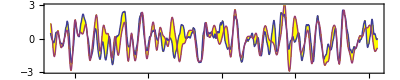

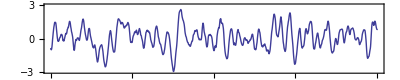

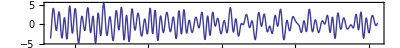

-Graphics-

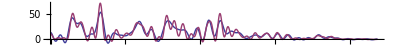

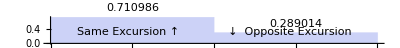

```mathematica
(* NUMBER 3  applied to NINO34 *)
(* ################################### From data ##################################### *)
WinLowFilter = 215;    WinHiFilter = 10;  (* 8 *)
R = 2.2*(MeanFilter[NINO34[[All,2]],WinHiFilter] - MeanFilter[NINO34[[All,2]],WinLowFilter]); 
STRT=2; STRTY=1880+STRT/12; SEP=0.0; LNGTH=1603; ENDY=1880+LNGTH/12; (* 1603 STRT=590;   STRTY=1880+STRT/12; SEP=0.0; LNGTH=1190; ENDY=1880+LNGTH/12; *)
SOIT = Table[{1880+i/12, -0.97*R[[i]]+SEP},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 2.197;  dilate[x_] := -(0.2*Sin[0.074*x-0.5]+0.0*Cos[2*Pi*x-0.2]);
OSC := 9.08;     TR=52.01;
Hill[x_] := CF+0.355*tsi[x-1.55]*(1.03+0.62*qbo[x+0.43])  ;
Osc[x_] := 0.534*(Cos[2*Pi/OSC*x+4.45]-Cos[4*Pi/OSC*x+2.18]) +0.438*Cos[2*Pi/7.3*x+0.47] - 0.356*Cos[2*Pi*x/27.3-0.6];
RHS[x_] :=+ 2.9*(0.8219*qbo[x+0.71]*(0.98+0.16*tsi[x+0.62])-0.438*cw[x+0.04]+0.0082*tsi[x+3.9]+0.01+0.0001*x );  
SOLN=NDSolve[{y''[x]+Hill[x]*y[x] == RHS[x-0.07],  y'[TR]==-0.12, y[TR]==+0.04}, y, {x, 0, 260}];   
SOIM=Table[{1880.0+x, Osc[x]+0.12*tsi'[x-4.4]-0.12*qbo[x-0.6]+First[-0.68*y[1.00091*x+dilate[x]+0.73] /. SOLN]},{x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-3,3+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
SDIF = SOIT[[All,2]]-SOIM[[All,2]];  
ListLinePlot[SDIF, PlotRange->{-3,3}, Frame->True, Axes->True, PlotLegends->{"SOI-Model"}, AspectRatio->0.2] 
RHSD = Table[{1880+i/12, RHS[i/12]},{i,STRT,LNGTH,1}];
ListLinePlot[{RHSD}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"RHS"}]
HillD = Table[{1880+i/12, Hill[i/12]},{i,STRT,LNGTH,1}];
ListLinePlot[{HillD}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"Hill"}]
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,800,1200,400}],{ω,0,π/12},PlotRange->All,AspectRatio->0.1]
SBIN = Abs[Sign[SOIT[[All,2]]]- Sign[SOIM[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.05,  ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
```

{char t,4.23901,0.0215803, Years from,1880.17,to,2013.58,CC,52.8682,52.8899,0.0216449}

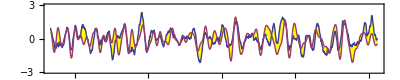

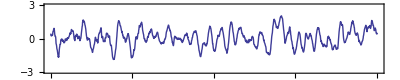

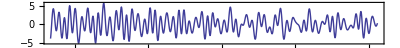

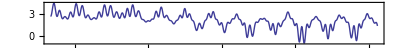

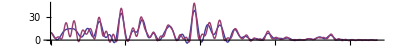

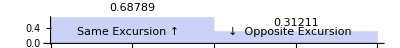

```mathematica
(* NUMBER 3  *)
(* ################################### From data ##################################### *)
WinLowFilter = 214;    WinHiFilter = 11;  (* 8 *)
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter]-1*MeanFilter[darwin[[All,2]],WinLowFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]-1*MeanFilter[tahiti[[All,2]],WinLowFilter]); 
STRT=2; STRTY=1880+STRT/12; SEP=0.0; LNGTH=1603; ENDY=1880+LNGTH/12; (* 1603 STRT=590;   STRTY=1880+STRT/12; SEP=0.0; LNGTH=1190; ENDY=1880+LNGTH/12; *)
SOIT = Table[{1880+i/12, -0.92*R[[i]]+SEP},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 2.197;  dilate[x_] := -(0.19*Sin[0.074*x-0.5]+0.0*Cos[2*Pi*x-0.2]);
OSC := 9.08;     TR=52.01;
Hill[x_] := CF+0.37*tsi[x-1.6]*(1.03+0.61*qbo[x+0.43])  ;
Osc[x_] := 0.534*(Cos[2*Pi/OSC*x+4.45]-Cos[4*Pi/OSC*x+2.18]) +0.438*Cos[2*Pi/7.3*x+0.47] - 0.356*Cos[2*Pi*x/27.3-0.6];
RHS[x_] :=+ 3.1*(0.82*qbo[x+0.71]*(0.98+0.16*tsi[x+0.62])-0.438*cw[x+0.04]+0.0082*tsi[x+3.9]-0.04*tsi'[x+4.7] +0.011+0.0001*x );  
SOLN=NDSolve[{y''[x]+Hill[x]*y[x] == RHS[x-0.08],  y'[TR]==-0.02, y[TR]==+0.03}, y, {x, 0, 260}];   
SOIM=Table[{1880.0+x, 0*Osc[x]-0.123*qbo[x-0.6]+First[-0.48*y[1.0009*x+dilate[x]+0.66] /. SOLN]},{x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-3,3+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
SDIF = SOIT[[All,2]]-SOIM[[All,2]];  
ListLinePlot[SDIF, PlotRange->{-3,3}, Frame->True, Axes->True, PlotLegends->{"SOI-Model"}, AspectRatio->0.2] 
RHSD = Table[{1880+i/12, RHS[i/12]},{i,STRT,LNGTH,1}];
ListLinePlot[{RHSD}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"RHS"}]
HillD = Table[{1880+i/12, Hill[i/12]},{i,STRT,LNGTH,1}];
ListLinePlot[{HillD}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"Hill"}]
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,800,1200,400}],{ω,0,π/12},PlotRange->All,AspectRatio->0.1] 
SBIN = Abs[Sign[SOIT[[All,2]]]- Sign[SOIM[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.05,  ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
```